```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap1D[];
sizes={1024};
timeStep=0.001;
k=-0.4;
contactInteractionFactor=4 Pi k;
max=10ho;
min=-10ho;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{1024} | 1 | 1024 | {10} | {-10} | {20/1023} | {(1023 π)/10240} | {(1023 π)/20}

time | energies | moments | misc
(0) | (total | -0.502651
kinetic | 0.25
potential | 0.25
contact | -1.00265
virial | -1.00265) | (meanX | 0
sigmaX | 0.707107
norm | 1.) | (steps | 0
A0 | 0.751126)

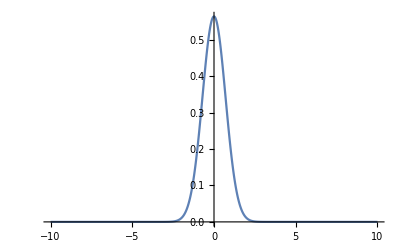

```mathematica
calcAllTable
p1=plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",10,10]]
```

{2.9321,Null}

time | energies | moments | misc
(10.) | (total | -0.991697
kinetic | 1.15541
potential | 0.0580686
contact | -2.20517
virial | -0.0104966) | (meanX | 0
sigmaX | 0.340789
norm | 1.) | (steps | 10000
A0 | 1.14402)

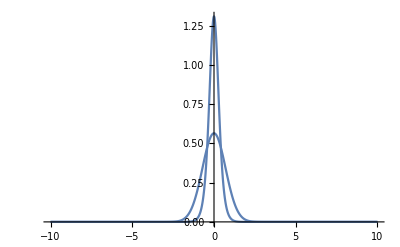

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All]
```

```mathematica
reportMoments
```

time | meanX | sigmaX | norm
0 | 0 | 0.707107 | 1.
1. | 0 | 0.36095 | 1.
2. | 0 | 0.341444 | 1.
3. | 0 | 0.34081 | 1.
4. | 0 | 0.34079 | 1.
5. | 0 | 0.340789 | 1.
6. | 0 | 0.340789 | 1.
7. | 0 | 0.340789 | 1.
8. | 0 | 0.340789 | 1.
9. | 0 | 0.340789 | 1.
10. | 0 | 0.340789 | 1.

Turn off harmonic potential

```mathematica
newPotential[free];
plot:=AppendTo[lplots,{time,plotProjections}];
reset[];
myPrint=Null&;
AbsoluteTiming[evolve["rte",40,200,200]]
```

{27.2855,Null}

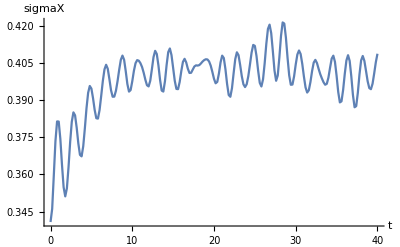

```mathematica
plotM["sigmaX"]
```

```mathematica
Show[lplots[[All,2]],PlotRange->All]
```

-Graphics-